```mathematica
$Assumptions={n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,NN>0,σ>0,s>0,z∈ Reals,px2∈ Reals,py2∈ Reals,px1∈ Reals,py1∈ Reals,px∈ Reals,py∈ Reals,r∈ Reals,r1∈ Reals,r2∈ Reals,x1∈ Reals,x2∈ Reals,x∈ Reals,w∈ Reals,t∈ Reals,k1∈ Reals,k2∈ Reals,k∈ Reals,n∈ Reals,q∈ Reals,a∈ Reals,d∈ Reals,p∈ Reals,p1∈ Reals,p2∈ Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,NN∈Reals}
```

{n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,NN>0,σ>0,s>0,z∈Reals,px2∈Reals,py2∈Reals,px1∈Reals,py1∈Reals,px∈Reals,py∈Reals,r∈Reals,r1∈Reals,r2∈Reals,x1∈Reals,x2∈Reals,x∈Reals,w∈Reals,t∈Reals,k1∈Reals,k2∈Reals,k∈Reals,n∈Reals,q∈Reals,a∈Reals,d∈Reals,p∈Reals,p1∈Reals,p2∈Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,NN∈Reals}

```mathematica
yyyHankSingle[x_,y_,t_,k_,w_]:=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t])/(11),{d,-7,7,1.4}]
```

```mathematica
DaForceSingleX[x_,y_,t_,k_,w_] = -D[yyyHankSingle[x,y,t,k,w],x];
DaForceSingleY[x_,y_,t_,k_,w_] = -D[yyyHankSingle[x,y,t,k,w],y];
CosDisSqWidth = ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]
GaussianTanDisSqWidth[d_,σ_] = ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]
SincSqWidth[d_] = ProbabilityDistribution[Sinc[x π/(d)]^2/d,{x,-π/2,π/2}]
```

ProbabilityDistribution[Cos[x]^2/2,{x,-π/2,π/2}]

ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]

ProbabilityDistribution[Sinc[(x π)/d]^2/d,{x,-π/2,π/2}]

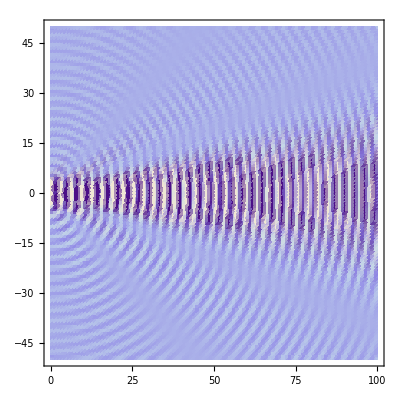

```mathematica
DensityPlot[yyyHankSingle[x,y,0,2,2],{x,0,100},{y,-50,50},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

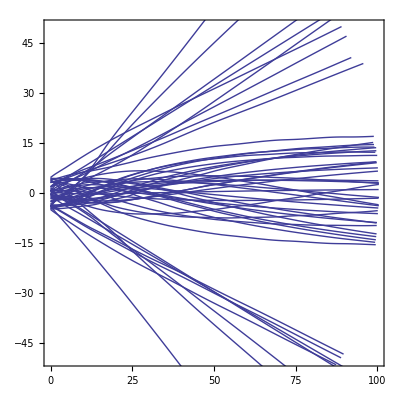

```mathematica
AAA =  1.0;
ddd = 5.0;
x000 = 0.0;
www=2;
v000 = 1.0;
kkk= 2;
disss = 0.0;
tmax = 100;
NMAX=50;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-ddd,ddd}]],y'[0]== v000 Sin[RandomVariate[GaussianTanDisSqWidth[π/2,1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU},{t,0,tmax},PlotRange->{{0,tmax},{-tmax/2,tmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
Integrate[ⅇ^(ⅈ (k-k0)^2 t+ⅈ k x) Sinc[d k],{k,-∞,∞}]
```

$Aborted

```mathematica
FullSimplify[(1/d(1/2+ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]-ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])))(1/d(1/2-ⅈ/2) π (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)]+ⅈ (FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])))]
```

1/(2 d^2)π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2)

```mathematica
Integrate[1/(2 d^2)π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2),{x,-∞,∞}]
```

$Aborted

```mathematica
probdens[x_,t_,d_]:=1/(2 d^2)π^2 ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2)
```

```mathematica
probdensk[x_,t_,k_,d_]:=1/(2 d^2)π^2 ((FresnelC[(k(d-x))/(√(2 π) √t)]+FresnelC[(k(d+x))/(√(2 π) √t)])^2+(FresnelS[(k(d-x))/(√(2 π) √t)]+FresnelS[(k(d+x))/(√(2 π) √t)])^2)
```

```mathematica
probdenskw[x_,t_,k_,w_,d_]:=1/(2 d^2)π^2 ((FresnelC[(k(d-x))/(√(2 π) √(w t))]+FresnelC[(k(d+x))/(√(2 π) √(w t))])^2+(FresnelS[(k(d-x))/(√(2 π) √(w t))]+FresnelS[(k(d+x))/(√(2 π) √(w t))])^2)
```

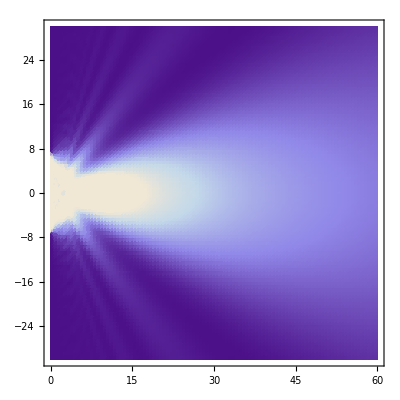

```mathematica
DensityPlot[probdens[y,x,7],{x,0,60},{y,-30,30},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

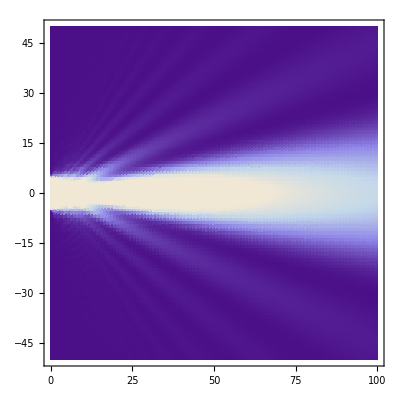

```mathematica
DensityPlot[probdensk[y,x,2,5],{x,0,100},{y,-50,50},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

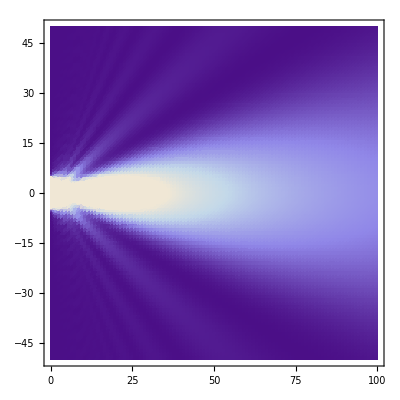

```mathematica
DensityPlot[probdenskw[y,x,2,2,5],{x,0,100},{y,-50,50},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

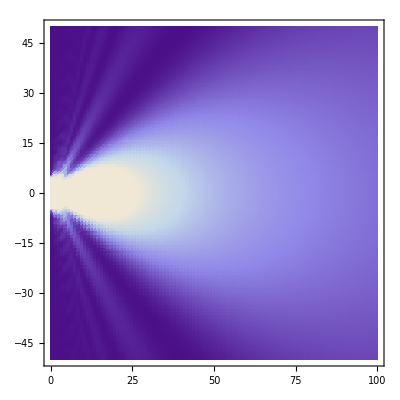

```mathematica
DensityPlot[probdenskw[y,x,1,1,5],{x,0,100},{y,-50,50},PlotPoints->{100,100},ClippingStyle->Automatic,BaseStyle->{FontFamily->"Times",FontSize->14},AspectRatio->1]
```

```mathematica
VelocityField3[x_, t_, d_ ]:=-(√(2/π) Sin[(d x)/(2 t)] (Cos[(d^2+x^2)/(4 t)] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) Sin[(d^2+x^2)/(4 t)]))/(√t ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))
```

```mathematica
VelocityField4[x_, t_,k_,w_ ,d_ ]:=-(√(2/π) Sin[(k d x)/(2 w t)] (Cos[(k^2(d^2+x^2))/(4 w t)] (FresnelC[(k(d-x))/(√(2 π) √(w t))]+FresnelC[(k(d+x))/(√(2 π) √(w t))])+(FresnelS[(k(d-x))/(√(2 π) √(w t))]+FresnelS[(k(d+x))/(√(2 π) √(w t))]) Sin[(k^2(d^2+x^2))/(4 w t)]))/(√(w t) ((FresnelC[(k(d-x))/(√(2 π) √(w t))]+FresnelC[(k(d+x))/(√(2 π) √(w t))])^2+(FresnelS[(k(d-x))/(√(2 π) √(w t))]+FresnelS[(k(d+x))/(√(2 π) √(w t))])^2))
```

```mathematica
VelocityField5[x_, t_,k_,d_ ]:=-(√(2/π) Sin[(k d x)/(2  t)] (Cos[(k^2(d^2+x^2))/(4  t)] (FresnelC[(k(d-x))/(√(2 π) √t)]+FresnelC[(k(d+x))/(√(2 π) √t)])+(FresnelS[(k(d-x))/(√(2 π) √t)]+FresnelS[(k(d+x))/(√(2 π) √t)]) Sin[(k^2(d^2+x^2))/(4 t)]))/(√t ((FresnelC[(k(d-x))/(√(2 π) √t)]+FresnelC[(k(d+x))/(√(2 π) √t)])^2+(FresnelS[(k(d-x))/(√(2 π) √t)]+FresnelS[(k(d+x))/(√(2 π) √t)])^2))
```

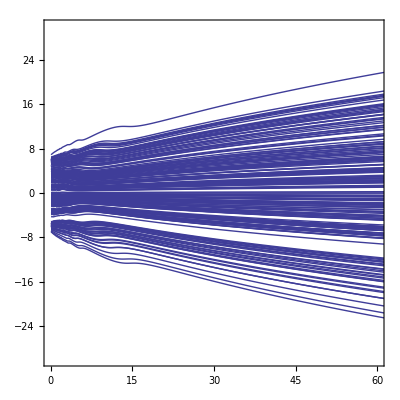

```mathematica
ddd = 7.0;
www=1.0;
kkk = 1.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==-VelocityField3[y[t], t, ddd ]2,y[0.1]== RandomVariate[UniformDistribution[{-ddd,ddd}]]},y,{t,0.1,70}],{200}];
Plot[{(y[t])/.HollandtablU},{t,0.1,70}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
$Aborted
```

$Aborted

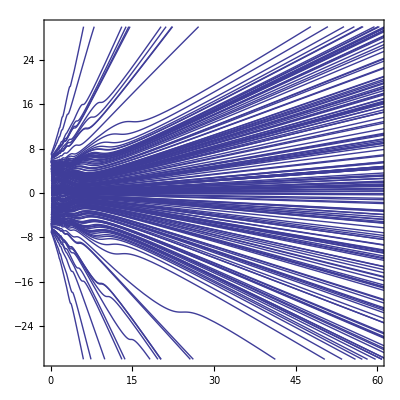

```mathematica
ddd = 7.0;
www=1.0;
kkk = 1.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==-VelocityField3[y[t], t, ddd ]2,y[0.1]== RandomVariate[UniformDistribution[{-ddd,ddd}]]},y,{t,0.1,70}],{200}];
Plot[{(y[t])/.HollandtablU},{t,0.1,70}, PlotRange->{{0,60},{-30,30}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA =  1.0;
WIDTHVALUE =7;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.005;
tmax = 200;
swidth = 1;
phase = -π;
CHUNK = 100;
REPEAT = 100;
CUTTOFF = 160;
WIDTHLIST = {2,4,6,8,10};



Close["HydroSingleSlitC160W"<> ToString[WIDTHVALUE]<>".dat"]



Do[

outstream=OpenAppend["HydroSingleSlitC160W"<> ToString[WIDTHVALUE]<>".dat"];

Hollandtabl3DU=
Parallelize[Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t+phase,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t+phase,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-WIDTHVALUE,WIDTHVALUE}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth ]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}]
,{CHUNK}]
];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=80,ttt < tmax, ttt+=0.1, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
Close[outstream]
,{REPEAT}];
```

HydroSingleSlitC160W7.dat

$Aborted